# NG^23 T_01. Многослойный персептрон

КМ2021, курс 2, семестр 4
Ковалевская В.С.
09-фев-2023

## Задание 1

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll[kmANN21];
kmANN21[W_?VectorQ]@{x1_,x2_}:=UnitStep[W.{x1,x2,1}];
```

```mathematica
ClearAll[kmANN221];
kmANN221[{{W11_,W12_}?MatrixQ,W2_?VectorQ}]@{x1_,x2_}:=UnitStep[W2.{UnitStep[W11.{x1,x2,1}],UnitStep[W12.{x1,x2,1}],1}];
```

```mathematica
ClearAll[kmANN211];
kmANN211[{W1_?VectorQ,W2_?VectorQ}]@{x1_,x2_}:=UnitStep[W2.{x1,UnitStep[W1.{x1,x2,1}],x2,1}];
```

```mathematica
NN = kmANN21@{2,3,11}
```

kmANN21[{2,3,11}]

```mathematica
NN@{2,-33}
```

0

```mathematica
NN221 = kmANN221@{{{1,5,6},{4, 8,11}},{5,6,7}}
```

kmANN221[{{{1,5,6},{4,8,11}},{5,6,7}}]

```mathematica
NN221@{4,7}
```

1

```mathematica
kmANN221[{{{1,2,3},{3,2,1}},{3,3,0}}]@{22,-11}
```

1

```mathematica
kmANN211[{{1,2,3},{4,3,2,0.5}}]@{22,-11}
```

1

```mathematica
NN = kmANN21@{1,1,-.5}
Show[-Graphics-,DensityPlot[NN@{x,y},{x,-1,2},{y,-1,2},ImageSize->200,GridLines->Automatic,ColorFunction->(If[#<0.5,Opacity[0,Gray],Opacity[0.4,Gray]]&)]]
```

kmANN21[{1,1,-0.5}]

-Graphics-

```mathematica
NN = kmANN221@{{{0,1,0.5},{1, 1,-.1}},{1,0,0.5}};
Show[-Graphics-,DensityPlot[NN@{x,y},{x,-1,2},{y,-1,2},ImageSize->200,GridLines->Automatic,ColorFunction->(If[#<0.5,Opacity[0,Gray],Opacity[0.4,Gray]]&)]]
```

-Graphics-

```mathematica
BooleDS = Flatten[Table[{x,y},{x,0,1},{y,0,1}],1]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
kmANN21[{-1,-1,-1}]@{1,1}
```

0

## Задание 2

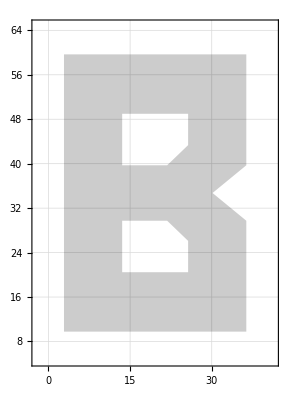
{В,-Graphics-,{{2.8512,59.6727},{36.3528,59.6727},{36.3528,39.7143},{30.1492,34.7247},{36.3528,29.7351},{36.3528,9.77672},{2.8512,9.77672},{25.6608,48.9807},{13.5432,48.9807},{13.5432,39.7143},{21.8072,39.7143},{25.6608,43.3451},{13.5432,29.7351},{13.5432,20.4687},{25.6608,20.4687},{25.6608,26.1043},{21.8072,29.7351}}}

```mathematica
{Letter, FigLetter,Vertices} = Apply[{First@#1, Uncompress@Last@#1,{##2}}&,Import["NG23T01Problem.xlsx",{"Sheets","Ковалевская Варвара"}]]
```

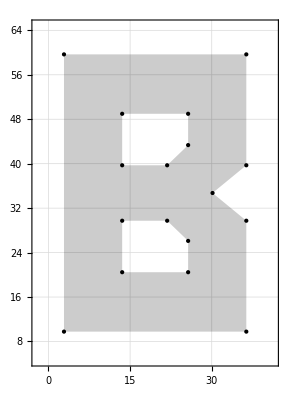

```mathematica
Show[FigLetter,Graphics[{Point@Vertices}]]
```

```mathematica
Vertices
Vertices+0.1
```

{{2.8512,59.6727},{36.3528,59.6727},{36.3528,39.7143},{30.1492,34.7247},{36.3528,29.7351},{36.3528,9.77672},{2.8512,9.77672},{25.6608,48.9807},{13.5432,48.9807},{13.5432,39.7143},{21.8072,39.7143},{25.6608,43.3451},{13.5432,29.7351},{13.5432,20.4687},{25.6608,20.4687},{25.6608,26.1043},{21.8072,29.7351}}

{{2.9512,59.7727},{36.4528,59.7727},{36.4528,39.8143},{30.2492,34.8247},{36.4528,29.8351},{36.4528,9.87672},{2.9512,9.87672},{25.7608,49.0807},{13.6432,49.0807},{13.6432,39.8143},{21.9072,39.8143},{25.7608,43.4451},{13.6432,29.8351},{13.6432,20.5687},{25.7608,20.5687},{25.7608,26.2043},{21.9072,29.8351}}

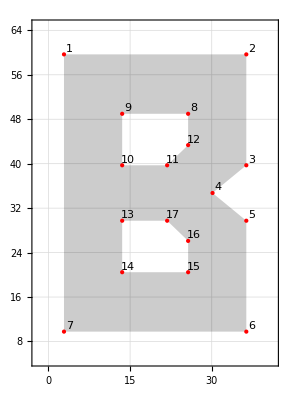

```mathematica
Fig2 = Show[FigLetter,Graphics[{MapIndexed[Text[First@#2,#1]&,Vertices+1],PointSize[Large],Red,Point@Vertices}]]
```

```mathematica
((x-x1)/(x2-x1)-(y-y1)/(y2-y1)) (y2-y1) (x2-x1)==0;
Collect[%,{x,y},Together]
```

(x1-x2) y+x2 y1-x1 y2+x (-y1+y2)==0

```mathematica
ClearAll[Neuron];
Neuron[{{x1_,y1_},{x2_,y2_}}]:=Block[{w1,w2,w},w = {w1=y1-y2,w2=x2-x1,-x2 y1+x1 y2};Expand[w/√(w1^2+w2^2)]]
```

```mathematica
Neuron[{{1,1},{-11,100}}]
```

{-33/(√1105),-4/(√1105),37/(√1105)}

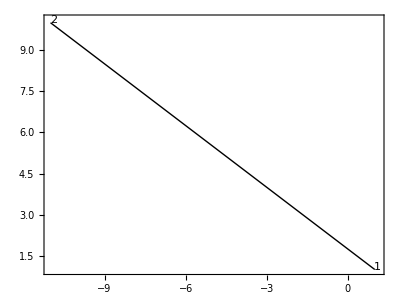

```mathematica
{{1,1},{-11,10}};
Graphics[{PointSize@Large,MapIndexed[Text[First@#2,#1]&,%+0.1],Line@%},ImageSize->{Automatic,200},Frame->True]
```

```mathematica
Apply[{-#2,#1}&,{-11,10}-{1,1}]
```

{-9,-12}

```mathematica
{-11,10}-{1,1}
```

{-12,9}

```mathematica
Graphics[HalfPlane[{{1,1},{-11,10}},Apply[{-#2,#1}&,{-11,10}-{1,1}]]]
```

-Graphics-

```mathematica
ClearAll[kmHalfPlane];
kmHalfPlane[{P1_,P2_}]:=HalfPlane[{P1,P2},Apply[{-#2,#1}&,P2-P1]]
```

```mathematica
pnt = {{1,1},{-10,10}};
w=Neuron[pnt];
Graphics[{PointSize@Large,MapIndexed[Text[First@#2,#1]&,pnt+0.1],Line@pnt,Opacity[0.3,Magenta],kmHalfPlane@pnt,Opacity[1,Black],Arrow[{#,#+w[[;;2]]}&[Mean@pnt]]},ImageSize->{Automatic,200},Frame->True,GridLines->Automatic]
```

-Graphics-

```mathematica
Fig2
```

-Graphics-

```mathematica
num = {{2,1},{1,7},{7,6},{6,2},{5,4},{4,3},{10,9},{9,8},{8,12},{12,11},{11,10},{13,17},{17,16},{15,14}}
```

{{2,1},{1,7},{7,6},{6,2},{5,4},{4,3},{10,9},{9,8},{8,12},{12,11},{11,10},{13,17},{17,16},{15,14}}

```mathematica
Vertices
```

{{2.8512,59.6727},{36.3528,59.6727},{36.3528,39.7143},{30.1492,34.7247},{36.3528,29.7351},{36.3528,9.77672},{2.8512,9.77672},{25.6608,48.9807},{13.5432,48.9807},{13.5432,39.7143},{21.8072,39.7143},{25.6608,43.3451},{13.5432,29.7351},{13.5432,20.4687},{25.6608,20.4687},{25.6608,26.1043},{21.8072,29.7351}}

```mathematica
kmHalfPlane@{{2.8512,59.672720000000005},{36.3528,59.672720000000005}}
```

HalfPlane[{{2.8512,59.6727},{36.3528,59.6727}},{0.,33.5016}]

```mathematica
Show[Fig2,Graphics[{Hue[0.7,1.7,0.9,.1],kmHalfPlane@{{2.8512,59.672720000000005},{36.3528,59.672720000000005}}}]]
```

-Graphics-

```mathematica
MapIndexed[#->First@#2&,num]
```

{{2,1}→1,{1,7}→2,{7,6}→3,{6,2}→4,{5,4}→5,{4,3}→6,{10,9}→7,{9,8}→8,{8,12}→9,{12,11}→10,{11,10}→11,{13,17}→12,{17,16}→13,{15,14}→14}

```mathematica
Manipulate[Show[Fig2,Graphics[{Hue[0.7,1.7,0.9,.1],kmHalfPlane@Vertices[[n]]}]],Row[{Control@{{n,First@num,"HalfPlane"},MapIndexed[#->First@#2&,num],SetterBar}}]]
```

Part::partd: Part specification Vertices⟦{2,1}⟧ is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in Show[Fig2,].

## Задание 3

```mathematica
w
```

{-9/(√202),-11/(√202),10 √(2/101)}

```mathematica
Sign[w.Append[#,1]]&
%@{9,4}
```

Sign[w.Append[#1,1]]&

-1

```mathematica
ClearAll[kmANN];
kmANN[W_?VectorQ]:=Sign[W.Append[#,1]]&
```

```mathematica
((x-x1)/(x2-x1)-(y-y1)/(y2-y1)) (y2-y1) (x2-x1)==0;
Collect[%,{x,y},Together]
```

(x1-x2) y+x2 y1-x1 y2+x (-y1+y2)==0

```mathematica
ClearAll[Neuron];
Neuron[{{x1_,y1_},{x2_,y2_}}]:=Block[{w1,w2,w},w = {w1=y1-y2,w2=x2-x1,-x2 y1+x1 y2};Expand[w/√(w1^2+w2^2)]]
```

```mathematica
Vertices
```

{{2.8512,59.6727},{36.3528,59.6727},{36.3528,39.7143},{30.1492,34.7247},{36.3528,29.7351},{36.3528,9.77672},{2.8512,9.77672},{25.6608,48.9807},{13.5432,48.9807},{13.5432,39.7143},{21.8072,39.7143},{25.6608,43.3451},{13.5432,29.7351},{13.5432,20.4687},{25.6608,20.4687},{25.6608,26.1043},{21.8072,29.7351}}

```mathematica
num
```

{{2,1},{1,7},{7,6},{6,2},{5,4},{4,3},{10,9},{9,8},{8,12},{12,11},{11,10},{13,17},{17,16},{15,14}}

```mathematica
MapIndexed[#->First@#2&,num][[1,1]]
```

{2,1}

```mathematica
Vertices[[{2,1}]]
```

{{36.3528,59.6727},{2.8512,59.6727}}

```mathematica
Neuron@Vertices[[{2,1}]]
```

{0.,-1.,59.6727}

```mathematica
MapIndexed[#->First@#2&,num]
```

{{2,1}→1,{1,7}→2,{7,6}→3,{6,2}→4,{5,4}→5,{4,3}→6,{10,9}→7,{9,8}→8,{8,12}→9,{12,11}→10,{11,10}→11,{13,17}→12,{17,16}→13,{15,14}→14}

```mathematica
Neuron@Vertices[[#]]&/@num
```

{{0.,-1.,59.6727},{1.,0.,-2.8512},{0.,1.,-9.77672},{-1.,0.,36.3528},{-0.62674,-0.779228,45.9542},{-0.62674,0.779228,-8.16276},{-1.,0.,13.5432},{0.,1.,-48.9807},{1.,0.,-25.6608},{0.685758,-0.727829,13.9508},{0.,-1.,39.7143},{0.,1.,-29.7351},{0.685758,0.727829,-36.5966},{0.,-1.,20.4687}}

```mathematica
Neuron@Vertices[[#]]&/@num
MapIndexed[#->First@#2&,%]
```

{{0.,-1.,59.6727},{1.,0.,-2.8512},{0.,1.,-9.77672},{-1.,0.,36.3528},{-0.62674,-0.779228,45.9542},{-0.62674,0.779228,-8.16276},{-1.,0.,13.5432},{0.,1.,-48.9807},{1.,0.,-25.6608},{0.685758,-0.727829,13.9508},{0.,-1.,39.7143},{0.,1.,-29.7351},{0.685758,0.727829,-36.5966},{0.,-1.,20.4687}}

{{0.,-1.,59.6727}→1,{1.,0.,-2.8512}→2,{0.,1.,-9.77672}→3,{-1.,0.,36.3528}→4,{-0.62674,-0.779228,45.9542}→5,{-0.62674,0.779228,-8.16276}→6,{-1.,0.,13.5432}→7,{0.,1.,-48.9807}→8,{1.,0.,-25.6608}→9,{0.685758,-0.727829,13.9508}→10,{0.,-1.,39.7143}→11,{0.,1.,-29.7351}→12,{0.685758,0.727829,-36.5966}→13,{0.,-1.,20.4687}→14}

```mathematica
First@num
```

{2,1}

```mathematica
weight = Neuron@Vertices[[#]]&/@num;
Thread[%->num]
```

{{0.,-1.,59.6727}→{2,1},{1.,0.,-2.8512}→{1,7},{0.,1.,-9.77672}→{7,6},{-1.,0.,36.3528}→{6,2},{-0.62674,-0.779228,45.9542}→{5,4},{-0.62674,0.779228,-8.16276}→{4,3},{-1.,0.,13.5432}→{10,9},{0.,1.,-48.9807}→{9,8},{1.,0.,-25.6608}→{8,12},{0.685758,-0.727829,13.9508}→{12,11},{0.,-1.,39.7143}→{11,10},{0.,1.,-29.7351}→{13,17},{0.685758,0.727829,-36.5966}→{17,16},{0.,-1.,20.4687}→{15,14}}

```mathematica
Export1=Prepend[MapThread[Join,{num,weight}],{"From","To","W1","W2","W0"}]
```

{{From,To,W1,W2,W0},{2,1,0.,-1.,59.6727},{1,7,1.,0.,-2.8512},{7,6,0.,1.,-9.77672},{6,2,-1.,0.,36.3528},{5,4,-0.62674,-0.779228,45.9542},{4,3,-0.62674,0.779228,-8.16276},{10,9,-1.,0.,13.5432},{9,8,0.,1.,-48.9807},{8,12,1.,0.,-25.6608},{12,11,0.685758,-0.727829,13.9508},{11,10,0.,-1.,39.7143},{13,17,0.,1.,-29.7351},{17,16,0.685758,0.727829,-36.5966},{15,14,0.,-1.,20.4687}}

```mathematica
Export["NG4T01 KavaleuskayaVarvara.xlsx","Layer1"->Export1,"FormattedData"]
```

NG4T01 KavaleuskayaVarvara.xlsx

```mathematica
kmANN@weight[[1]]
DensityPlot[%@{x1,x2},{x1,0,15},{x2,0,15},ImageSize->200,GridLines->Automatic,ColorFunction->(If[#>0,Opacity[0,Blue],Opacity[.3,Blue]]&)]
```

Sign[{0.,-1.,59.6727}.Append[#1,1]]&

-Graphics-

```mathematica
Show[Fig2,DensityPlot[kmANN[weight[[2]]]@{x1,x2},{x1,-10,70},{x2,-10,70},ImageSize->200,GridLines->Automatic,ColorFunction->(If[#>0,Opacity[0.3,Blue],Opacity[0,Blue]]&)]]
```

-Graphics-

```mathematica
Manipulate[Show[Fig2, DensityPlot[kmANN[weight[[n]]]@{x1, x2}, {x1,0,70},{x2,0,70}, ImageSize -> 200, GridLines -> Automatic, ColorFunction -> (If[# > 0, Opacity[.3, Blue], Opacity[0, Blue]] &)], PlotLabel -> weight[[n]]], {n, Range[Length[weight]], SetterBar},ControlPlacement->Top]
```

Part::partd: Part specification weight⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Fig2,,PlotLabel→weight⟦1⟧].

## Задание 4

```mathematica
ClearAll[kmANN];
kmANN[W_?VectorQ]:=Sign[W.Append[#,1]]&;
kmANN[W_?MatrixQ]:=Sign[W.Append[#,1]]&;
```

```mathematica
sign = kmANN[weight[[#]]]&/@Range[Length[weight]]
```

{Sign[{0.,-1.,59.6727}.Append[#1,1]]&,Sign[{1.,0.,-2.8512}.Append[#1,1]]&,Sign[{0.,1.,-9.77672}.Append[#1,1]]&,Sign[{-1.,0.,36.3528}.Append[#1,1]]&,Sign[{-0.62674,-0.779228,45.9542}.Append[#1,1]]&,Sign[{-0.62674,0.779228,-8.16276}.Append[#1,1]]&,Sign[{-1.,0.,13.5432}.Append[#1,1]]&,Sign[{0.,1.,-48.9807}.Append[#1,1]]&,Sign[{1.,0.,-25.6608}.Append[#1,1]]&,Sign[{0.685758,-0.727829,13.9508}.Append[#1,1]]&,Sign[{0.,-1.,39.7143}.Append[#1,1]]&,Sign[{0.,1.,-29.7351}.Append[#1,1]]&,Sign[{0.685758,0.727829,-36.5966}.Append[#1,1]]&,Sign[{0.,-1.,20.4687}.Append[#1,1]]&}

```mathematica
%[[1]]@{0,1}
```

1

```mathematica
kmANN[weight[[1]]]@{0,3}
```

1

```mathematica
Grid[{Range[Length[weight]],Range[Length[weight]]}]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14

```mathematica
kmANN[weight[[#]]]&/@Range[Length[weight]]
```

{Sign[{0.,-1.,59.6727}.Append[#1,1]]&,Sign[{1.,0.,-2.8512}.Append[#1,1]]&,Sign[{0.,1.,-9.77672}.Append[#1,1]]&,Sign[{-1.,0.,36.3528}.Append[#1,1]]&,Sign[{-0.62674,-0.779228,45.9542}.Append[#1,1]]&,Sign[{-0.62674,0.779228,-8.16276}.Append[#1,1]]&,Sign[{-1.,0.,13.5432}.Append[#1,1]]&,Sign[{0.,1.,-48.9807}.Append[#1,1]]&,Sign[{1.,0.,-25.6608}.Append[#1,1]]&,Sign[{0.685758,-0.727829,13.9508}.Append[#1,1]]&,Sign[{0.,-1.,39.7143}.Append[#1,1]]&,Sign[{0.,1.,-29.7351}.Append[#1,1]]&,Sign[{0.685758,0.727829,-36.5966}.Append[#1,1]]&,Sign[{0.,-1.,20.4687}.Append[#1,1]]&}

```mathematica
points = Thread[{Range[0,Length[weight]-1],Range[0,Length[weight]-1]}]
```

{{0,0},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13}}

```mathematica
sign[[1]]@points[[1]]
```

1

```mathematica
n = 1;
While[n<14,sign[[n]]@points[[n]];n++]
```

```mathematica
DensityPlot[kmANN[weight[[1]]]@{x1, x2}, {x1,0,70},{x2,0,70}, ImageSize -> 200, GridLines -> Automatic, ColorFunction -> (If[# > 0, Opacity[.3, Blue], Opacity[0, Blue]] &)]
```

-Graphics-

## Задание 5

```mathematica
Manipulate[Show[Fig2, DensityPlot[kmANN[weight[[n]]]@{x1, x2}, {x1,0,70},{x2,0,70}, ImageSize -> 200, GridLines -> Automatic, ColorFunction -> (If[# > 0, Opacity[.3, Blue], Opacity[0, Blue]] &)], PlotLabel -> weight[[n]]], {n, Range[Length[weight]], SetterBar},ControlPlacement->Top]
```

Part::partd: Part specification weight⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Fig2,,PlotLabel→weight⟦1⟧].

```mathematica
L2 = {{1,3,2,4},{-5,-6},{-7,-9,-8,-10,-11},{-7,-9,-12,-13,-14}}
```

{{1,3,2,4},{-5,-6},{-7,-9,-8,-10,-11},{-7,-9,-12,-13,-14}}

```mathematica
L2 = {#1∧#3∧#2∧#4&,¬#5∧¬#6&,¬#7∧¬#9∧¬#8∧¬#10∧¬#11&,¬#7∧¬#9∧¬#12∧¬#13∧¬#14&};
```

```mathematica
R1=kmHalfPlane@Vertices[[#]]&/@num;
```

```mathematica
R2=BooleanRegion[#,R1]&/@L2;
```

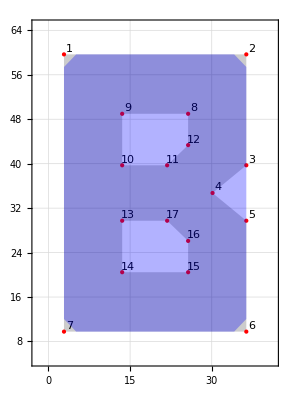

```mathematica
Show[Fig2,Region[Style[BooleanRegion[L2[[1]],R1],Opacity[.3,Blue]]]]
```

```mathematica
Manipulate[Show[Fig2,Region[Style[BooleanRegion[n,R1],Opacity[.3,Blue]]]],{{n,First@L2},Thread[L2->Range@Length@L2],SetterBar},ControlPlacement->Top,AppearanceElements->None]
```

BooleanRegion::rglst: R1 should be a non-empty list of regions.

Region::reg: BooleanRegion[#1&&#3&&#2&&#4&,R1] is not a correctly specified region.

Show::gcomb: Could not combine the graphics objects in Show[Fig2,Region[BooleanRegion[#1&&#3&&#2&&#4&,R1]]].

```mathematica
L3=#1∧(¬#2∧¬#3∧¬#4)&
```

#1&&(!#2&&!#3&&!#4)&

```mathematica
R2=BooleanRegion[#,R1]&/@L2;
```

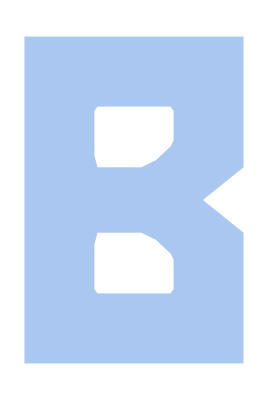

```mathematica
Show[Region[BooleanRegion[L3,R2]]]
```

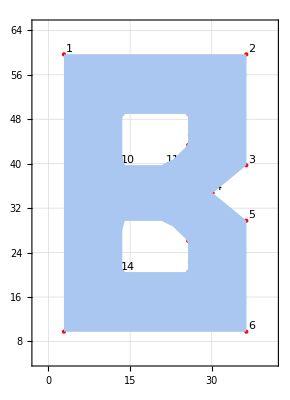

```mathematica
Show[Fig2,Region[BooleanRegion[L3,R2]]]
```

## Задание 6

```mathematica
ClearAll[kmANN];
kmANN[W_?VectorQ]:=Sign[W.Append[#,1]]&;
kmANN[W_?MatrixQ]:=Sign[W.Append[#,1]]&;
kmANN[W:{__?MatrixQ}]:=Function[x,Fold[kmANN[#2]@#1&,x,W]];
```

```mathematica
L2
```

{#1&&#3&&#2&&#4&,!#5&&!#6&,!#7&&!#9&&!#8&&!#10&&!#11&,!#7&&!#9&&!#12&&!#13&&!#14&}

```mathematica
w2=({{1, 1, 1, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, -3.5}, {0, 0, 0, 0, -1, -1, 0, 0, 0, 0, 0, 0, 0, 0, -1.5}, {0, 0, 0, 0, 0, 0, -1, -1, -1, -1, -1, 0, 0, 0, -4.5}, {0, 0, 0, 0, 0, 0, -1, 0, -1, 0, 0, -1, -1, -1, -4.5}})
```

{{1,1,1,1,0,0,0,0,0,0,0,0,0,0,-3.5},{0,0,0,0,-1,-1,0,0,0,0,0,0,0,0,-1.5},{0,0,0,0,0,0,-1,-1,-1,-1,-1,0,0,0,-4.5},{0,0,0,0,0,0,-1,0,-1,0,0,-1,-1,-1,-4.5}}

```mathematica
pol = {{#1&&#3&&#2&&#4&},{!#5&&!#6&},{!#7&&!#9&&!#8&&!#10&&!#11&},{!#7&&!#9&&!#12&&!#13&&!#14&}};
```

```mathematica
Export2=Prepend[MapThread[Join,{pol,w2}],{"Polygon","W1","W2","W3","W4","W5","W6","W7","W8","W9","W10","W11","W12","W13","W14","W0"}];
```

```mathematica
Export["NG4T01 KavaleuskayaVarvara.xlsx",{"Layer1"->Export1,"Layer2"->Export2}]
```

NG4T01 KavaleuskayaVarvara.xlsx

## Задание 7

```mathematica
L3
```

#1&&(!#2&&!#3&&!#4)&

```mathematica
w3={1,-1,-1,-1,-3.5}
```

{1,-1,-1,-1,-3.5}

```mathematica
Export3=Prepend[MapThread[Join,{{{L3}},{w3}}],{"Polygon","W1","W2","W3","W4","W0"}];
```

```mathematica
Export["NG4T01 KavaleuskayaVarvara.xlsx",{"Layer1"->Export1,"Layer2"->Export2,"Layer3"->Export3}]
```

NG4T01 KavaleuskayaVarvara.xlsx

```mathematica
ANN=kmANN@{weight,w2,{w3}};
```

```mathematica
ANN@{20,45}
```

{-1}

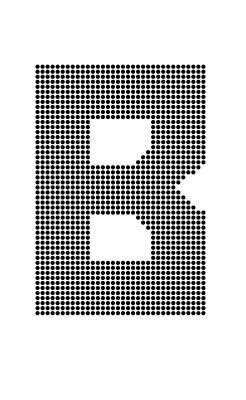

```mathematica
Graphics[{Table[{If[ANN[{x,y}][[1]]<1,White,Black],Point@{x,y}},{x,0,40},{y,0,65}]}]
```